In the present notebook we examine the  inflationary viability of a scalar field minimally coupled to a rescaled Einstein-Hilbert Gravity, aR. First, we define the potential of the scalar field as function of the inflaton, in this case a E-Model. Then, we calculate the slow-roll indices for this potential using the expressions we have derived from the Friedmann equations for this specific type of modified gravity. Then, we solve the equation ϵ1=1 with respect to ϕ, to obtain its valu at the end of inflation and use it in the expression of the e-folding number to find the initial value of ϕ. Moving on, we calculate the slow-roll indiced and observational parameters, that is the spectral index of scalar perturbations and the tensor to scalar ratio, as functions of the model’s free parameters and the e-folding number. We set  N=60 e-foldings and search for which values of the free parameters the Planck 2018 constraints on the spectral index and tensor to scalar ratio can be satisfied, while the slow-roll inflation approximations hold true as well.

```mathematica
The potential under examination is:
```

```mathematica
V[ϕ_]:= V0 (1-Exp[-k ϕ (2/(3 μ))^(1/2)])^2
```

```mathematica
The slow-roll indices are:
```

```mathematica
ϵ=1/(2k^2) (V'[ϕ]/V[ϕ])^2 //Simplify
```

4/(3 (-1+ⅇ^(√(2/3) k √(1/μ) ϕ))^2 μ)

```mathematica
η=1/k^2 (V''[ϕ]/V[ϕ]) //Simplify
```

-(4 (-2+ⅇ^(√(2/3) k √(1/μ) ϕ)))/(3 (-1+ⅇ^(√(2/3) k √(1/μ) ϕ))^2 μ)

```mathematica
ϵ1=α ϵ
```

(4 α)/(3 (-1+ⅇ^(√(2/3) k √(1/μ) ϕ))^2 μ)

```mathematica
ϵ2=-α η +ϵ1 //Simplify
```

-(4 α)/(3 μ-3 ⅇ^(√(2/3) k √(1/μ) ϕ) μ)

```mathematica
The expressions of ϕf and ϕi are:
```

```mathematica
Solve[ϵ1==1, ϕ]
```

{{ϕ→ConditionalExpression[(√(3/2) (2 ⅈ π C[1]+Log[(-2 √3 √α+3 √μ)/(3 √μ)]))/(k √(1/μ)),C[1]∈ℤ]},{ϕ→ConditionalExpression[(√(3/2) (2 ⅈ π C[1]+Log[(2 √3 √α+3 √μ)/(3 √μ)]))/(k √(1/μ)),C[1]∈ℤ]}}

```mathematica
ϕf=(√(3/2)Log[(2 √3 √α+3 √μ)/(3 √μ)])/(k √(1/μ))
```

(√(3/2) Log[(2 √3 √α+3 √μ)/(3 √μ)])/(k √(1/μ))

```mathematica
Integrate[-k^2/α (V[ϕ]/V'[ϕ]),ϕ] //Expand
```

-(3 ⅇ^(√(2/3) k √(1/μ) ϕ) μ)/(4 α)+(√(3/2) k ϕ)/(2 α √(1/μ))

```mathematica
Solve[Y==-(3 ⅇ^(√(2/3) k √(1/μ) ϕf) μ)/(4 α)+(3 ⅇ^(√(2/3) k √(1/μ) ϕ) μ)/(4 α),ϕ]
```

{{ϕ→ConditionalExpression[(√(3/2) (2 ⅈ π C[1]+Log[(4 Y α+2 √3 √α √μ+3 μ)/(3 μ)]))/(k √(1/μ)),C[1]∈ℤ]}}

```mathematica
ϕi=(√(3/2) Log[(4 Y α+2 √3 √α √μ+3 μ)/(3 μ)])/(k √(1/μ))
```

(√(3/2) Log[(4 Y α+2 √3 √α √μ+3 μ)/(3 μ)])/(k √(1/μ))

```mathematica
The expressions of the slow-roll and observational indices for ϕ=ϕi, i.e at the beginning of inflation, are:
```

The first potential slow-roll parameter:

```mathematica
ϵi=ϵ/. ϕ-> ϕi //Simplify
```

(3 μ)/(α (2 Y √α+√3 √μ)^2)

```mathematica
Series[(3 μ)/(α (2 Y √α+√3 √μ)^2),{Y,Infinity,2}]  //Simplify
```

(3 μ)/(4 α^2 Y^2)+O[1/Y]^3

```mathematica
ϵi=(3 μ)/(4 α^2 Y^2)
```

(3 μ)/(4 Y^2 α^2)

The second potential slow-roll parameter:

```mathematica
ηi=η/. ϕ-> ϕi //Simplify
```

(-4 Y α-2 √3 √α √μ+3 μ)/(α (2 Y √α+√3 √μ)^2)

```mathematica
Series[(-4 Y α-2 √3 √α √μ+3 μ)/(α (2 Y √α+√3 √μ)^2),{Y,Infinity,2}]
```

-1/(α Y)+((√3 √μ)/(2 α^(3/2))+(3 μ)/(4 α^2))/Y^2+O[1/Y]^3

```mathematica
ηi=-1/(α Y)+((√3 √μ)/(2 α^(3/2))+(3 μ)/(4 α^2))/Y^2
```

-1/(Y α)+((√3 √μ)/(2 α^(3/2))+(3 μ)/(4 α^2))/Y^2

The first Hubble slow-roll parameter:

```mathematica
ϵ1i=ϵ1 /. ϕ-> ϕi //Simplify
```

(3 μ)/(2 Y √α+√3 √μ)^2

```mathematica
Series[(3 μ)/(2 Y √α+√3 √μ)^2,{Y,Infinity,2}]
```

(3 μ)/(4 α Y^2)+O[1/Y]^3

```mathematica
ϵ1i=(3 μ)/(4 α Y^2)
```

(3 μ)/(4 Y^2 α)

The second Hubble slow-roll parameter:

```mathematica
ϵ2i=ϵ2 /. ϕ-> ϕi //Simplify
```

(2 √α)/(2 Y √α+√3 √μ)

```mathematica
Series[ϵ2i,{Y,Infinity,2}]
```

1/Y-(√3 √μ)/(2 √α Y^2)+O[1/Y]^3

```mathematica
ϵ2i=1/Y-(√3 √μ)/(2 √α Y^2)
```

1/Y-(√3 √μ)/(2 Y^2 √α)

The spectral index of scalar perturbations:

```mathematica
ns=1-6α ϵi +2α ηi //Simplify
```

(-2 Y α+Y^2 α+√3 √α √μ-3 μ)/(Y^2 α)

The tensor to scalar ratio:

```mathematica
r=16α ϵi
```

(12 μ)/(Y^2 α)

## The variable Y denotes the e-foldings number, represented as N in the literature. Now, we set Y=60, as we usually assume that the universe has grown approximately e^60 times. In the following we examine for which values of the free parameters, α and μ, this potential satisfies the Planck 2018 constraints: ns=[0.9607,0.9691] and r<0.056. Furthermore, we shall check if the slow-roll conditions are also satisfied.

```mathematica
About the spectral index of primordial curvature perturbations, ns:
```

The first method is algebraically:

```mathematica
ns60=ns/. Y-> 60 //Simplify
```

(3480 α+√3 √α √μ-3 μ)/(3600 α)

I set: √(α/μ)= x, thus the expression of the spectral index at the beginning of inflation assuming the latter lasted for Y=60 e-foldings, becomes:

```mathematica
ns60'= (3480 x^2+√3 √x -3)/(3600 x^2)
```

(-3+√3 √x+3480 x^2)/(3600 x^2)

```mathematica
Solve[ns60'==0.9691,x]
Solve[ns60'==0.9607,x]
```

{{x→0.090839-0.493077 ⅈ},{x→0.090839+0.493077 ⅈ}}

{{x→-0.373763-0.0662036 ⅈ},{x→-0.373763+0.0662036 ⅈ},{x→0.308072}}

```mathematica
(* when the solution of one of these equations is a not a real number, it means that the spectral index does not take this value for any set of values of the model's free parameters. *)
```

```mathematica
Limit[ns60',x-> Infinity] //N
```

0.966667

```mathematica
pn1=Plot[ns60',{x,0.289,0.9},PlotStyle->97,Frame-> True,FrameLabel->{Sqrt[α/μ], "Spectral Index ns"}];
```

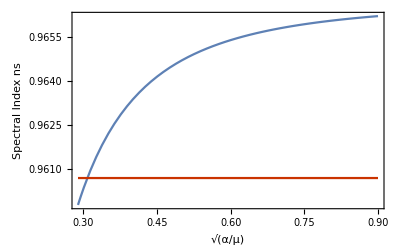

```mathematica
pn2=Plot[0.9607,{x,0.289,0.9},PlotStyle->112,Frame-> True];
pn3=Show[pn1,pn2]
```

The second method is via contour plots:

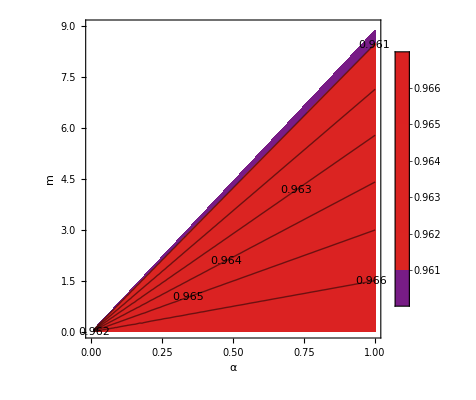

```mathematica
ContourPlot[(3480 α+√3 √α √μ-3 μ)/(3600 α),{α,0,1},{μ,0.01,9},Frame->True,ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0.9607,0.9691},FrameLabel->{"α","m"}]
```

```mathematica
About the tensor to scalar ratio, r:
```

The first method is algebraically:

```mathematica
r60=r/. Y-> 60
```

μ/(300 α)

I set: √(α/μ)= x, thus the expression of the tensor to scalar ratio at the beginning of inflation assuming the latter lasted for Y=60 e-foldings, becomes:

```mathematica
r60'=1/(300 x^2)
```

1/(300 x^2)

```mathematica
Reduce[r60'<0.056 && x>0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>0.243975

```mathematica
pr1=Plot[r60',{x,0.24,0.9},PlotStyle->97,Frame-> True,FrameLabel->{Sqrt[α/μ], "Tensor to Scalar Ratio r"}];
```

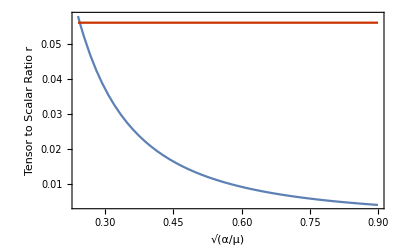

```mathematica
pr2=Plot[0.056,{x,0.24,0.9},PlotStyle->112,Frame-> True];
Show[pr1,pr2]
```

The second method is via contour plots:

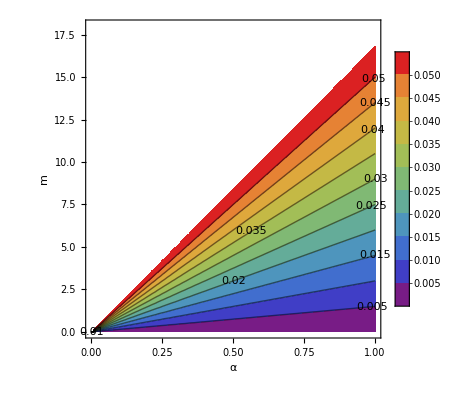

```mathematica
ContourPlot[r60,{α,0,1},{μ,10^(-6),18},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10,PlotRange->{0,0.056}]
```

```mathematica
About the first slow-roll index,ϵ1:
```

The first method is algebraically:

```mathematica
ϵ160=ϵ1i/. Y-> 60
```

μ/(4800 α)

I set: √(α/μ)= x

```mathematica
ϵ160'=1/(4800 x^2)
```

1/(4800 x^2)

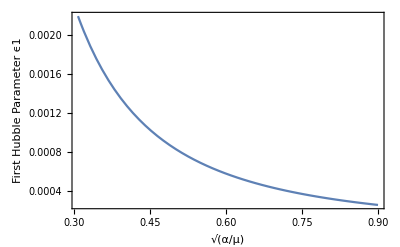

```mathematica
Plot[ϵ160',{x,0.30807246996710647,0.9},PlotStyle->97,Frame-> True,FrameLabel->{Sqrt[α/μ], "First Hubble Parameter ϵ1"}]
```

The second method is via contour plots:

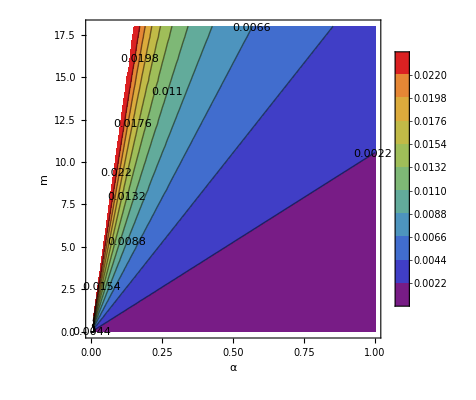

```mathematica
ContourPlot[μ/(4800 α),{α,0,1},{μ,10^(-6),18},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10]
```

```mathematica
(* The slow-roll approximation ϵ1<1 is satisfied for this range of values of the free parameters, that also satisfy the Planck contraints on ns and r *)
```

```mathematica
About the second slow-roll index,ϵ2:
```

The first method is algebraically:

```mathematica
ϵ260=ϵ2i/. Y-> 60
```

1/60-(√μ)/(2400 √3 √α)

I set: √(α/μ)= x

```mathematica
ϵ260'=1/60-1/(2400 √3 x)
```

1/60-1/(2400 √3 x)

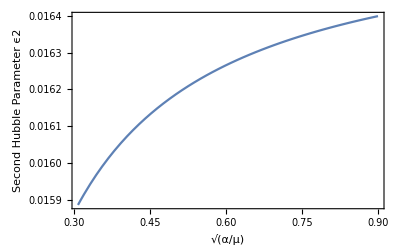

```mathematica
Plot[ϵ260',{x,0.30807246996710647,0.9},PlotStyle->97,Frame-> True,FrameLabel->{Sqrt[α/μ], "Second Hubble Parameter ϵ2"}]
```

```mathematica
Limit[1/60-1/(2400 √3 x), x-> Infinity] //N
```

0.0166667

The second method is via contour plots:

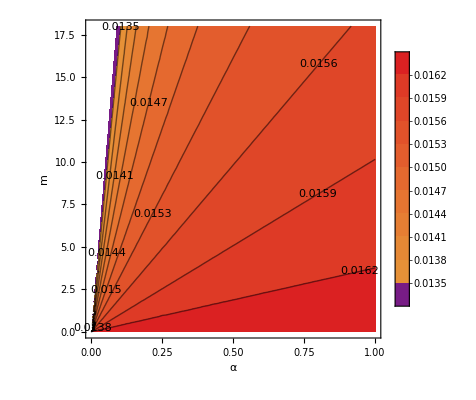

```mathematica
ContourPlot[1/60-(√μ)/(2400 √3 √α),{α,0,1},{μ,10^(-6),18},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10]
```

```mathematica
(* The slow-roll approximation ϵ2<1 is also satisfied for this range of values of the free parameters, that also satisfy the Planck contraints on ns and r *)
```

```mathematica
About the potential slow-roll index,ϵ:
```

```mathematica
ϵi60=ϵi/. Y-> 60
```

μ/(4800 α^2)

```mathematica
Reduce[μ/(4800 α^2)<0.01 && α>0 && μ>0,α]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

μ>0&&α>0.144338 √μ

I set: α^2/μ= z

```mathematica
Reduce[1/(4800 z)<0.01 && z>0 ,z]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

z>0.0208333

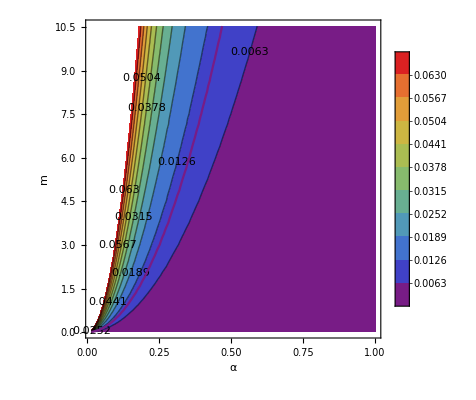

```mathematica
pe11=ContourPlot[μ/(4800 α^2),{α,0.0144338,1},{μ,10^(-2),10.5364},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10];
pe22=ContourPlot[μ/(4800 α^2)==0.01,{α,0.0144338,1},{μ,10^(-2),10.5364},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10];
pe=Show[pe11,pe22]
```

```mathematica
About the potential slow-roll index,η:
```

```mathematica
ηi60=ηi/. Y-> 60 //Simplify
```

(-240 α+2 √3 √α √μ+3 μ)/(14400 α^2)

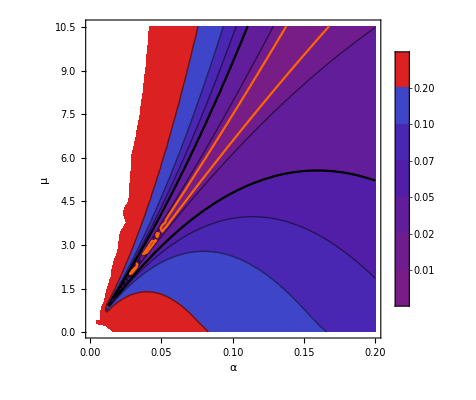

```mathematica
ph12=ContourPlot[Abs[(-240 α+2 √3 √α √μ+3 μ)/(14400 α^2)],{α,0.0949*10^(-2),0.2},{μ,10^(-2),10.5364},ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{α,μ},Contours-> {0.01,0.02,0.05,0.07,0.1,0.2}];
ph13=ContourPlot[Abs[(-240 α+2 √3 √α √μ+3 μ)/(14400 α^2)]==0.05,{α,0.0949*10^(-2),0.2},{μ,10^(-2),10.5364},PlotTheme->"GrayColor",PlotLegends->Automatic, FrameLabel->{α,μ},Contours-> {0.01,0.02,0.05,0.07,0.1,0.2}];ph14=ContourPlot[Abs[(-240 α+2 √3 √α √μ+3 μ)/(14400 α^2)]==0.01,{α,0.0949*10^(-2),0.2},{μ,10^(-2),10.5364},PlotTheme->"NeonColor",PlotLegends->Automatic, FrameLabel->{α,μ},Contours-> {0.01,0.02,0.05,0.07,0.1,0.2}];
ph14=Show[ph12,ph13,ph14]
```

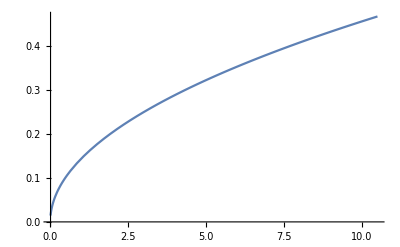

```mathematica
a=Plot[0.14433756729740646 √μ,{μ,10^(-2),10.5}]
```

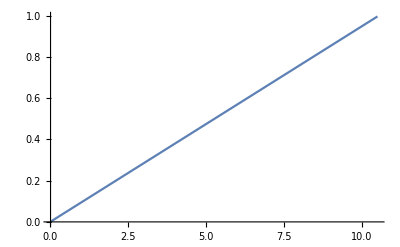

```mathematica
b=Plot[0.0949μ,{μ,10^(-2),10.5}]
```

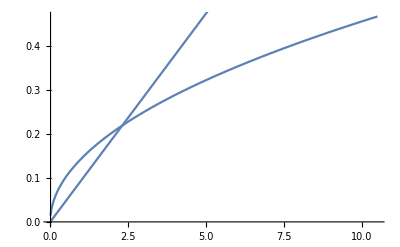

```mathematica
Show[a,b]
```

```mathematica
Solve[0.14433756729740646 √μ==0.0949μ,μ]
```

{{μ→0.},{μ→2.31327}}